√(25-(-5+x)^2)

{x,0,10}

(25 π)/2

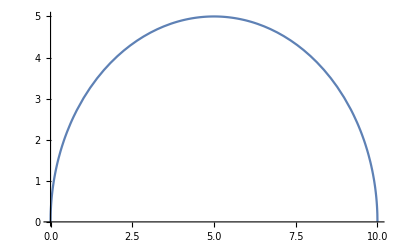

```mathematica
f=Sqrt[25-(x-5)^2]
bounds={x,0,10}
Integrate[f,bounds]
Plot[f,bounds]
```

x∈ℝ

Piecewise[{{2, 0<x<5}, {0, True}}]

{x,-∞,∞}

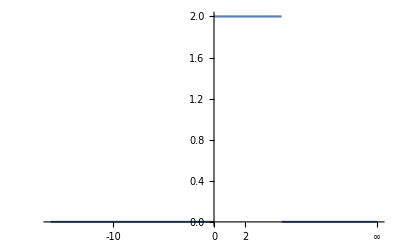

10

1/10

1/10 (Piecewise[{{2, 0<x<5}, {0, True}}])

True

5/2

25/12

Piecewise[{{1, x>5}, {x/5, 0<x≤5}, {0, True}}]

Piecewise[{{0, x<0}, {1/5, 0<x<5}, {0, x>5}, {Indeterminate, True}}]

Piecewise[{{1/5, 0<x<5}, {0, True}}]

```mathematica
$Assumptions=x∈ Reals
g=Piecewise[{{2,0<x<5},{0,True}}]
bounds={x,-Infinity,Infinity}
Plot[g,bounds]
A=Integrate[g,bounds]
k=1/A
f=k*g
Integrate[f,bounds]==1
EV=Integrate[x f,bounds]
Var=Integrate[(x-EV)^2f,bounds]
F=Integrate[f,{x,-Infinity,x}]
D[F,x]
f//Simplify
```

```mathematica
$Assumptions=x∈ Reals
g=Piecewise[{{Exp[-4x],0<=x<Infinity},{0,True}}]
bounds={x,-Infinity,Infinity}
Plot[g,bounds];
A=Integrate[g,bounds]
k=1/A
f=k*g
Integrate[f,bounds]==1
EV=Integrate[x f,bounds]
Var=Integrate[(x-EV)^2f,bounds]
F=Integrate[f,{x,-Infinity,x}]//Simplify
D[F,x]
f//FullSimplify
```

x∈ℝ

Piecewise[{{ⅇ^(-4 x), 0≤x<∞}, {0, True}}]

{x,-∞,∞}

1/4

4

4 (Piecewise[{{ⅇ^(-4 x), 0≤x<∞}, {0, True}}])

True

1/4

1/16

Piecewise[{{1-ⅇ^(-4 x), x>0}, {0, True}}]

Piecewise[{{0, x<0}, {4-4 ⅇ^(-4 x) (-1+ⅇ^(4 x)), x>0}, {Indeterminate, True}}]

4 (Piecewise[{{ⅇ^(-4 x), x≥0}, {0, True}}])

```mathematica
$Assumptions=x∈ Reals&&λ>0
f=Piecewise[{{λ Exp[-λ x],0<=x<Infinity},{0,True}}]
bounds={x,-Infinity,Infinity}
EV=Integrate[x f,bounds]
Var=Integrate[(x-EV)^2f,bounds]
{EV,Var}
```

x∈ℝ&&λ>0

Piecewise[{{ⅇ^(-x λ) λ, 0≤x<∞}, {0, True}}]

{x,-∞,∞}

1/λ

1/λ^2

{1/λ,1/λ^2}

```mathematica
$Assumptions=x∈ Reals&&σ>0;
f=1/Sqrt[2*π*σ^2] Exp[-1/2*((x-μ)/σ)^2];
bounds={x,-Infinity,Infinity}
EV=Integrate[x f,bounds]
Var=Integrate[(x-EV)^2f,bounds]
{EV,Var}
```

{x,-∞,∞}

μ

σ^2

{μ,σ^2}

```mathematica
$Assumptions=α>0&&β>0;
f=Piecewise[{{(β^α/Gamma[α]) x^(α-1) Exp[-β*x],0<=x<Infinity},{0,True}}]
bounds={x,-Infinity,Infinity}
EV=Integrate[x f,bounds]
Var=Integrate[(x-EV)^2f,bounds]
{EV,Var}
```

Piecewise[{{(ⅇ^(-x β) x^(-1+α) β^α)/Gamma[α], 0≤x<∞}, {0, True}}]

{x,-∞,∞}

α/β

α/β^2

{α/β,α/β^2}

```mathematica
$Assumptions=b>a;
f=Piecewise[{{1/(b-a),a<=x<=b},{0,True}}]
bounds={x,-Infinity,Infinity}
EV=Integrate[x f,bounds]
Var=Integrate[(x-EV)^2f,bounds]
{EV,Var}
```

Piecewise[{{1/(-a+b), a≤x≤b}, {0, True}}]

{x,-∞,∞}

(a+b)/2

1/12 (a-b)^2

{(a+b)/2,1/12 (a-b)^2}